## Functions

### General Functions

#### Sorting Data by Chromosome

```mathematica
nucleoMarkerSub[ftrs_]:=Transpose[
{
Transpose[ftrs][[1]],
Transpose[ftrs][[2]],
Transpose[ftrs][[3]],
Transpose[ftrs][[8]]
}
]
```

```mathematica
HistAlignRep[nucleosomeMarker_,chrs_]:=
Table[

SortBy[Select[nucleosomeMarker[[j]],#[[1]]==chrs[[i]]&],2]

,{i,1,Length[chrs]},{j,1,Length[nucleosomeMarker]}];
```

```mathematica
HistAlignRepSub[nucleosomeMarker_,chrs_]:=
Table[

nucleoMarkerSub[
SortBy[Select[nucleosomeMarker[[j]],#[[1]]==chrs[[i]]&],2]]

,{i,1,(Length[chrs]-1)},{j,1,Length[nucleosomeMarker]}];
```

#### Merge Functions

```mathematica
mergeChrPosExp[geneinf_,poslist_]:={geneinf[[1]],geneinf[[2]],geneinf[[3]],geneinf[[6]],geneinf[[7]],Select[poslist,#[[3]]==geneinf[[1]]&][[1,4]],Select[poslist,#[[3]]==geneinf[[1]]&][[1,5;;6]]}
```

### Sparse Matrix Functions

Generate sparse matrix with the features on some segment or whole chromosome. Length of segment is chrL, chrDomain is a list of start and end locations for a feature, and bpscale is the resolution. Note that the start and end

#### General Application

```mathematica
chrFeatureMap[chrL_,chrDomain_,bpscale_]:=
Total[
Table[
SparseArray[
i_/;
(Ceiling[chrDomain[[j,1]]])<i<(Ceiling[chrDomain[[j,2]]])->1,
Ceiling[chrL/bpscale],0
],{j,1,Length[chrDomain]}]
]
```

Below takes in the length of the chromosome, chrL_, a list of the domain coordinates in a paired list format of {start, stop}, a list of values, and the resolution to coarse grain to (bp_Scale)

```mathematica
chrFeatureMapValueScaled[chrL_,chrDomain_,val_,bpscale_ ]:=
Total[
Table[
SparseArray[
i_/;
Floor[chrDomain[[j,1]]/bpscale]<i<Ceiling[chrDomain[[j,2]]/bpscale]->val[[j]],
Ceiling[chrL/bpscale],0
],{j,1,Length[chrDomain]}]
]
```

mapToZeroMatrix [zeroMatrix_, dataMatrix_, normval_] :=

#### LAD Alignment

chrList is the index names for the chromosome element, chrLengths is a list of the lengths of each chromosome, lad1 is positions as a list of lists, lad2 is positions as a list of lists, bpscale is a scalar, defaulting to 1000 for resolution in Kb.

```mathematica
featureAlign[chrList_,chrLengths_, lad1_,lad2_,bpscale_]:=
Table[
{chrList[[ii]],
chrFeatureMap[
chrLengths[[ii]],
{#[[2]]/bpscale,#[[3]]/bpscale}&/@Select[lad1,StringMatchQ[#[[1]],chrList[[ii]]]&]
,bpscale
],
chrFeatureMap[
chrLengths[[ii]],
{#[[2]]/bpscale,#[[3]]/bpscale}&/@Select[lad2,StringMatchQ[#[[1]],chrList[[ii]]]&]
,bpscale
]
},
{ii,1,Length[chrList]}];
```

#### List of Feature Condition Alignment

```mathematica
featureAlignMultiple[chrList_,chrLengths_, chrft_,bpscale_]:=
Table[
{chrList[[ii]],
Table[
chrFeatureMap[
chrLengths[[ii]],
{#[[2]]/bpscale,#[[3]]/bpscale}&/@Select[chrft[[jj]],StringMatchQ[#[[1]],chrList[[ii]]]&]
,bpscale],{jj,1,Length[chrft]}]
},
{ii,1,Length[chrList]}];
```

#### Generate Empty Matrix

```mathematica
zeroMatrix[chromosome_,res_]:=Table[{res*i,res*j},{i,0,Ceiling[chromosome/res]},{j,0,Ceiling[chromosome/res]}]
```

### HiC Analysis Functions

#### Contact Scaling

```mathematica
distContact[hicData_]:=Transpose[{Transpose[hicData][[2]]-Transpose[hicData][[1]],Transpose[hicData][[3]]}];
```

```mathematica
scalingEst[tbl_,fn_]:={Transpose[tbl][[1,1]],fn[Transpose[tbl][[2]]]}
```

```mathematica
resScalingContacts[cond_,segs_]:=Table[MapIndexed[{#[[1]],#[[2]]/(segs)}&,cond[[i]]],{i,Length[cond]}]
```

resScalingContacts[cond_, segs_] := Table[MapIndexed[{#[[1]], #[[2]]/(segs*cond[[i, 1, 2]])} &, cond[[i]]], {i, Length[cond]}]

rescaling of the contacts is dividing the observed frequency / (number of segments in a chromosome * the contact count in the zero position)

```mathematica
resScalingContactsTotes[cond_]:=Table[MapIndexed[{#[[1]],#[[2]]/(Total[Transpose[cond[[i]]][[2]]])}&,cond[[i]]],{i,Length[cond]}]
```

```mathematica
resScalingContactsTotesSegments[cond_,totes_]:=Table[MapIndexed[{#[[1]],#[[2]]/totes[[i]]}&,cond[[i]]],{i,Length[cond]}]
```

### HiC to LAD Functions

#### Overlap Position

```mathematica
overlapHicLadIndex[hicIndex_,laminIndex_,lamidx_]:=
Flatten[Position[Table[hicIndex[[i,1,1]],{i,Length[hicIndex]}],_?(laminIndex[[lamidx,2]]<=#<=laminIndex[[lamidx,3]]&)],1]
```

```mathematica
overlapHicLadSelectByIndex[hicContacts_,hicidx_,lad_]:=Table[
Select[hicContacts[[hicidx[[i]]]],
((lad[[2]]<=#[[2]]<=lad[[3]]))&],
{i,Length[hicidx]}]
```

This is passing the contact matrix for a single chromosome for a single condition that has been arranged so that each segment is a subtable by the first position, hicidx is the position of a feature (in this class a position that contains values that fall within a LAD), and lad_ is the test coordinates (these can be anything of interest.

#### Overlap Values for start/end position

```mathematica
overlapHicLadSelect[hicValues_,laminIndex1_, laminIndex2_]:=
Select[Flatten[hicValues,1],(laminIndex1[[2]]<=#[[1]]<=laminIndex1[[3]])&&(laminIndex2[[2]]<=#[[2]]<=laminIndex2[[3]])&]
```

#### Scaling Measurement

```mathematica
lmFitHic[cond_,minidx_,maxidx_]:= Table[
LinearModelFit[Log@cond[[i,Position[cond[[i]],_?(#==minidx&)][[1,1]];;Position[cond[[i]],_?(#==maxidx&)][[1,1]]]], x,x]
,{i,Length[cond]}]
```

```mathematica
f0FitHic[lmvals_]:=Table[Normal[lmvals[[i]]]/.x->Log[x]//Exp,{i,Length[lmvals]}]
```

## Generated Data

### Already Generated

```mathematica
dir = SetDirectory@NotebookDirectory[]
```

#### HiC If Generated

```mathematica
tDone = FileNames["*.m",StringJoin[dir,"/Analysis/"],3];
```

```mathematica
tDone[[1]]
```

#### Load Data

```mathematica
chrToCheck =5;
tDoneChr = Select[tDone, StringContainsQ[StringJoin["/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]], ".m"]]]
```

```mathematica
allContactsVar = Import[Select[tDoneChr,StringContainsQ["All"]][[1]]];

acrossB1ChrVarAll = Import[Select[tDoneChr,StringContainsQ["acrossLad"]][[1]]];
acrossNotB1ChrVarAll = Import[Select[tDoneChr,StringContainsQ["acrossNotLad"]][[1]]];

withinB1ChrVarAll =  Import[Select[tDoneChr,StringContainsQ["withinLad"]][[1]]];
withinNotB1ChrVarAll = Import[Select[tDoneChr,StringContainsQ["withinNotLad"]][[1]]];
```

```mathematica
contDistCondMean = Table[scalingEst[allContactsVar[[i,j]],Total[#]&],{i,Length[allContactsVar]},{j,Length[allContactsVar[[i]]]}];
```

```mathematica
withinB1ChrVarDistSortMedian = Table[
scalingEst[withinB1ChrVarAll[[j,i]],Total[#]&],
{j,Length[withinB1ChrVarAll]},{i,Length[withinB1ChrVarAll[[j]]]}];

withinNotB1ChrVarDistSortMedian = Table[
scalingEst[withinNotB1ChrVarAll[[j,i]],Total[#]&],
{j,Length[withinNotB1ChrVarAll]},{i,Length[withinNotB1ChrVarAll[[j]]]}];

acrossB1ChrVarDistSortMedian = Table[
scalingEst[acrossB1ChrVarAll[[j,i]],Total[#]&],
{j,Length[acrossB1ChrVarAll]},{i,Length[acrossB1ChrVarAll[[j]]]}];

acrossNotB1ChrVarDistSortMedian = Table[
scalingEst[acrossNotB1ChrVarAll[[j,i]],Total[#]&],
{j,Length[acrossNotB1ChrVarAll]},{i,Length[acrossNotB1ChrVarAll[[j]]]}];
```

### Results across multiple chromosomes

```mathematica
scalingResultsByChromosome = Import["LAD Scaling.xlsx"];
```

```mathematica
scalingResultsByChromosome[[1,1,2;;]]
```

{1.026,0.902,0.872,0.856,0.857,0.879,0.899,0.909,0.905,0.902,0.939,0.934,0.844,0.915,0.891,0.966,1.102,0.904,1.084,1.027,0.992,1.035}

```mathematica
Table[scalingResultsByChromosome[[1,i,1]],{i,Length[scalingResultsByChromosome[[1]]]}]
```

{All Control,All KO,Lad Control,Lad KO,OutLad Control,OutLad KO}

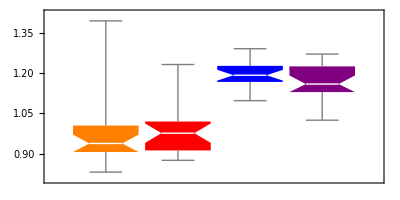

```mathematica
BoxWhiskerChart[{
scalingResultsByChromosome[[1,3,2;;]],
scalingResultsByChromosome[[1,4,2;;]],
scalingResultsByChromosome[[1,5,2;;]],
scalingResultsByChromosome[[1,6,2;;]]
} , "Notched",BarSpacing->Tiny,ChartStyle->{Orange,Red, Blue, Purple}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24], AxesOrigin->{7500,0}, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30]]
```

#### Fits to data

```mathematica
bothData = Flatten[{Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}],Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}]},1];
```

```mathematica
linearFitControl = LinearModelFit[
Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])}],x,x]
linearFitLbbNegative = LinearModelFit[
Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])}],x,x]
linearFitBoth = LinearModelFit[bothData,x,x]
```

```mathematica
inverseFitControl = NonlinearModelFit[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])}],a/x + b,{a,b},x]
inverseFitLbbNegative =NonlinearModelFit[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}]
,a/x + b,{a,b},x]
nonLinearBoth = NonlinearModelFit[bothData
,a/x + b,{a,b},x]
```

```mathematica
expFitControl = NonlinearModelFit[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])}],c+a*E^(- b*x),{a,b,c},x]

expFitLbbNegative =NonlinearModelFit[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}]
,c+a*E^(-b*x ),{a,b,c},x]
expLinearBoth = NonlinearModelFit[bothData
,c+a*E^(-b*x ),{a,b,c},x]
```

FittedModel[0.921829+2.817 ⅇ^(-0.086929 x)]

FittedModel[0.626578+0.692585 ⅇ^(-0.012358 x)]

FittedModel[0.869218+0.902469 ⅇ^(-0.0412415 x)]

```mathematica
expFitControl[0]
expLinearBoth[100]
```

3.73883

```mathematica
2.7/.884
```

3.0543

```mathematica
N[5/3]
```

1.66667

```mathematica
inverseFitLbbNegative["EstimatedVariance"]
inverseFitControl["EstimatedVariance"]
```

```mathematica
linearFitControl["RSquared"]
linearFitLbbNegative["RSquared"]
```

0.568316

0.496298

```mathematica
fitvals = linearFitBoth[#]&/@lbb1Coverage[[1;;22]];
fitvalsNonlinear = nonLinearBoth[#]&/@lbb1Coverage[[1;;22]];
fitvalsNonlinearLbb1 = inverseFitLbbNegative[#]&/@lbb1Coverage[[1;;22]];
fitvalsNonlinearControl = inverseFitControl[#]&/@lbb1Coverage[[1;;22]];
fitvalsExp = expLinearBoth[#]&/@lbb1Coverage[[1;;22]];
fitvalsExpLbb1 = expFitLbbNegative[#]&/@lbb1Coverage[[1;;22]];
fitvalsExpControl = expFitControl[#]&/@lbb1Coverage[[1;;22]];
```

```mathematica
chiCalcNonLinear[o_,e_] := Total[Table[(o[[i]]-e[[i]])^2/e[[i]],{i,Length[e]}]]
```

```mathematica
chiCalcNonLinear[scalingResultsByChromosome[[1,3,2;;]],fitvalsExp]
chiCalcNonLinear[scalingResultsByChromosome[[1,4,2;;]],fitvalsExp]
```

0.109913

0.0951995

```mathematica
chiCalcNonLinear[scalingResultsByChromosome[[1,3,2;;]],fitvalsExpControl]
chiCalcNonLinear[scalingResultsByChromosome[[1,4,2;;]],fitvalsExpLbb1]
```

0.097082

0.0842326

```mathematica
chiCalcNonLinear[scalingResultsByChromosome[[1,3,2;;]],fitvalsNonlinear]
chiCalcNonLinear[scalingResultsByChromosome[[1,4,2;;]],fitvalsNonlinear]
```

0.106493

0.0996564

```mathematica
chiCalcNonLinear[scalingResultsByChromosome[[1,3,2;;]],fitvalsNonlinearControl]
chiCalcNonLinear[scalingResultsByChromosome[[1,4,2;;]],fitvalsNonlinearLbb1]
```

0.0982392

0.0923696

```mathematica
Total[((#-Mean[(scalingResultsByChromosome[[1,3,2;;]])])^2)&/@scalingResultsByChromosome[[1,3,2;;]]]
Total[((#-Mean[(scalingResultsByChromosome[[1,4,2;;]])])^2)&/@scalingResultsByChromosome[[1,4,2;;]]]
```

0.328384

0.169011

Calculate R-squared for each condition compared to the data fit for both

```mathematica
1- Total[(fitvals-scalingResultsByChromosome[[1,3,2;;]])^2]/Total[((#-Mean[(scalingResultsByChromosome[[1,3,2;;]])])^2)&/@scalingResultsByChromosome[[1,3,2;;]]]
1- Total[(fitvals-scalingResultsByChromosome[[1,4,2;;]])^2]/Total[((#-Mean[(scalingResultsByChromosome[[1,4,2;;]])])^2)&/@scalingResultsByChromosome[[1,4,2;;]]]
```

0.552529

0.465625

#### Overlay fits with data

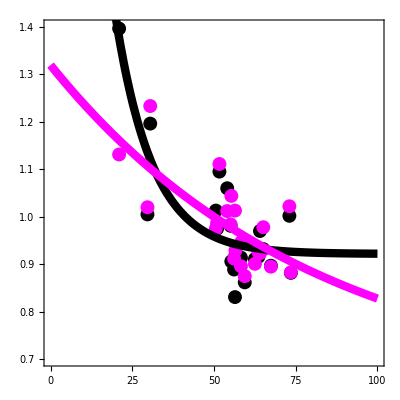

```mathematica
Show[{
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}],PlotStyle->{ Directive[Black, PointSize[.025]]}],
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}], PlotStyle->{ Directive[Magenta, PointSize[.025]]}],
Plot[expFitControl[x], {x,0,100}, PlotStyle->{ Directive[Black, Thickness[.015]]}],
Plot[expFitLbbNegative[x], {x,0,100}, PlotStyle->{ Directive[Magenta, Thickness[.015]]}]
},AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1,PlotRange->{{0,100},{.7,1.4}}, AspectRatio->1, Axes->None]
```

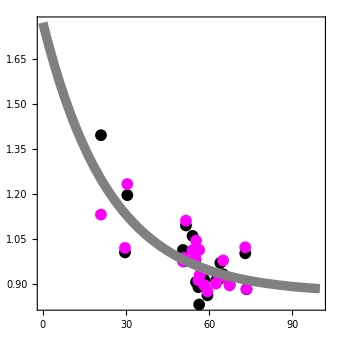

```mathematica
Show[{
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}], PlotStyle->{ Directive[Black, PointSize[.025]]}],
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}],PlotStyle->{ Directive[Magenta, PointSize[.025]]}],
Plot[expLinearBoth[x], {x,0,100}, PlotStyle->{ Directive[Gray, Thickness[.02]]}]
},AspectRatio->1,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], PlotRange->All , PlotRange->{{0,100},{0.7,1.6}}, Axes->None]
```

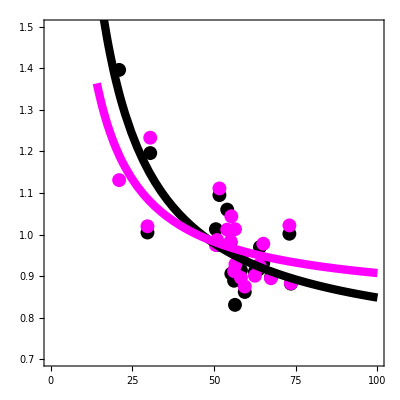

```mathematica
Show[{
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Black, PointSize[.025]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Magenta, PointSize[.025]], Directive[Blue, PointSize[.025]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
Plot[inverseFitControl[x], {x,10,100}, PlotStyle->{ Directive[Black, Thickness[.015]]}],
Plot[inverseFitLbbNegative[x], {x,10,100}, PlotStyle->{ Directive[Magenta, Thickness[.015]]}]
}, PlotRange->{{0,100},{0.7,1.5}},AxesStyle->Directive[Magenta,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1, AspectRatio->1, Axes-> None]
```

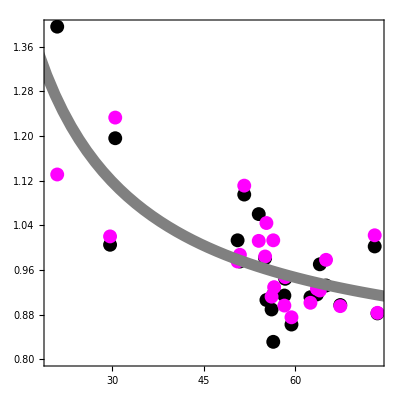

```mathematica
Show[{
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Black, PointSize[.025]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Magenta, PointSize[.025]], Directive[Blue, PointSize[.025]]}, AspectRatio->1,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
Plot[nonLinearBoth[x], {x,10,75}, PlotStyle->{ Directive[Gray, Thickness[.02]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1, PlotRange->All]
}, AspectRatio->1]
```

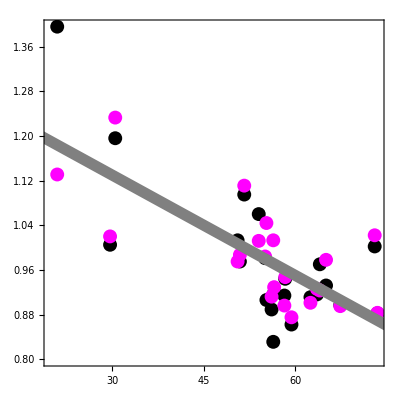

```mathematica
Show[{
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Black, PointSize[.025]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Magenta, PointSize[.025]], Directive[Blue, PointSize[.025]]}, AspectRatio->1,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
Plot[linearFitBoth[x], {x,10,75}, PlotStyle->{ Directive[Gray, Thickness[.02]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1, PlotRange->All]
}, AspectRatio->1]
```

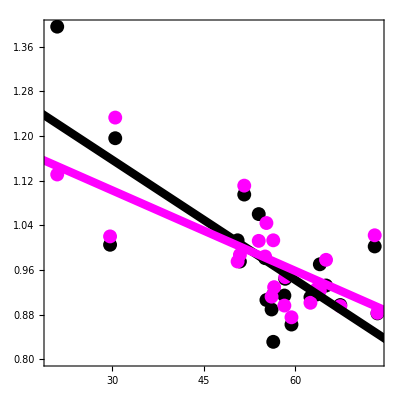

```mathematica
Show[{
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Black, PointSize[.025]]}, AspectRatio->1,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Magenta, PointSize[.025]], Directive[Blue, PointSize[.025]]}, AspectRatio->1,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
Plot[linearFitControl[x], {x,10,75}, PlotStyle->{ Directive[Black, Thickness[.015]]}, AspectRatio->1,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1, PlotRange->All],
Plot[linearFitLbbNegative[x], {x,10,75}, PlotStyle->{ Directive[Magenta, Thickness[.015]]}, AspectRatio->1,AxesStyle->Directive[Magenta,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1, PlotRange->All]
}, AspectRatio->1]
```

#### LB1 Coverage Vs Scaling

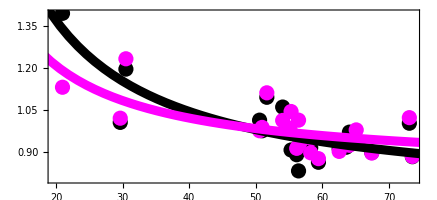

```mathematica
Show[{
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,3,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Black, PointSize[.025]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
ListPlot[Transpose[{lbb1Coverage[[1;;22]],
(scalingResultsByChromosome[[1,4,2;;]])
}], PlotRange->All,PlotStyle->{ Directive[Magenta, PointSize[.025]], Directive[Blue, PointSize[.025]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1],
Plot[inverseFitControl[x], {x,10,75}, PlotStyle->{ Directive[Black, Thickness[.015]]}, AspectRatio->Full,AxesStyle->Directive[Black,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1, PlotRange->All],
Plot[inverseFitLbbNegative[x], {x,10,75}, PlotStyle->{ Directive[Magenta, Thickness[.015]]}, AspectRatio->Full,AxesStyle->Directive[Magenta,Bold, 24],  Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30], AspectRatio->1, PlotRange->All]
}]
```

## Analysis of Contacts within specific markers

### Load LAD and HiC Data

```mathematica
dir = SetDirectory@NotebookDirectory[]
```

#### Lad Data

```mathematica
lamB1 = Import["/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/damid_HCT116/LaminB1/4DNFICCV71TZ.bed"];
lamB2 = Import["/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/damid_HCT116/LaminB2/4DNFIBQH62LX.bed"];
```

ladMatrix = Get[ "/Users/lma250/Documents/Research/Backman Lab/Lamin B Project/testlad"];

ladMatrix is to pull in a sparse matrix of Lbb1/Lbb2 LADs. This is a large file and is useful for visualization and potentially for hiC image production but for now do not load it.

```mathematica
byChrB1 = SplitBy[lamB1,#[[1]]&];
byChrB2 = SplitBy[lamB2,#[[1]]&];
```

```mathematica
byChrNotB1=Table[{byChrB1[[j,(i-1),1]],1+byChrB1[[j,(i-1),3]],byChrB1[[j,i,2]]-1},{j,1,Length[byChrB1]}, {i,2,Length[byChrB1[[j]]]}];
byChrNotB2=Table[{byChrB2[[j,(i-1),1]],1+byChrB2[[j,(i-1),3]],byChrB2[[j,i,2]]-1},{j,1,Length[byChrB2]}, {i,2,Length[byChrB2[[j]]]}];
```

Code below accounts for situations at start and end of chromosome. Run that once to append start and end info

#### General Organization

```mathematica
chrsLengths = Table[GenomeData[i,"SequenceLength"],{i,1,24}];
chrList =Flatten[Append[Table[StringJoin["chr",ToString[i]],{i,1,22}],{"chrX","chrY"}]];
chrList2 =Flatten[Append[Table[StringJoin["Chromosome",ToString[i]],{i,1,22}],{"ChromosomeX","ChromosomeY"}]];
chrList3  =Flatten[Append[Table[i,{i,1,22}],{"X","Y"}]];
m=1000;
```

```mathematica
chrsLengthsHg38 = {248956422,242193529,198295559,190214555,181538259,170805979,159345973,145138636,138394717,133797422,135086622,133275309,114364328,107043718,101991189,90338345,83257441,80373285,58617616,64444167,46709983,50818468,156040895,57227415};
```

chrsLengthsHg38 was input from https://www.ncbi.nlm.nih.gov/grc/human/data

```mathematica
chrsLengthsHg38[[chrToCheck]]
chrsLengthsHg38[[16;;18]]
```

181538259

{90338345,83257441,80373285}

#### General LAD Features

```mathematica
lbb1Coverage = Table[100*N[(Total[(#[[3]]-#[[2]])&/@byChrB1[[i]]])/chrsLengths[[i]]],{i,Length[chrsLengths]}];
lbb2Coverage = Table[100*N[(Total[(#[[3]]-#[[2]])&/@byChrB2[[i]]])/chrsLengths[[i]]],{i,Length[chrsLengths]}];
```

```mathematica
minMaxB1 =Table[MinMax[Select[Flatten[byChrB1[[i]]],NumericQ[#]&]],{i,Length[byChrB1]}];
minMaxB2 =Table[MinMax[Select[Flatten[byChrB2[[i]]],NumericQ[#]&]],{i,Length[byChrB2]}];
```

```mathematica
maxB1toExtendPos = Flatten[Position[Table[chrsLengthsHg38[[i]]-minMaxB1[[i,2]],{i,24}],_?(#>0&)]];
minB1toExtendPos=Flatten[Position[Table[minMaxB1[[i,1]],{i,24}],_?(#!=0&)]];
maxB2toExtendPos = Flatten[Position[Table[chrsLengthsHg38[[i]]-minMaxB2[[i,2]],{i,24}],_?(#>0&)]];
minB2toExtendPos=Flatten[Position[Table[minMaxB2[[i,1]],{i,24}],_?(#!=0&)]];
```

```mathematica
lbb1Coverage[[16;;18]]
```

{55.2983,30.4984,73.0584}

#### Adjust not-LAD areas to include start/stop of chromosomes (run only once)

```mathematica
Table[
AppendTo[
byChrNotB1[[maxB1toExtendPos[[i]]]]
,{chrList[[maxB1toExtendPos[[i]]]],minMaxB1[[maxB1toExtendPos[[i]],2]]+1,chrsLengthsHg38[[maxB1toExtendPos[[i]]]]}]
,{i,Length[maxB1toExtendPos]}];
```

```mathematica
Table[
AppendTo[
byChrNotB2[[maxB2toExtendPos[[i]]]]
,{chrList[[maxB2toExtendPos[[i]]]],minMaxB1[[maxB2toExtendPos[[i]],2]]+1,chrsLengthsHg38[[maxB2toExtendPos[[i]]]]}]
,{i,Length[maxB2toExtendPos]}];
```

```mathematica
Table[
PrependTo[byChrNotB1[[minB1toExtendPos[[i]]]],{chrList[[minB1toExtendPos[[i]]]],0,minMaxB1[[minB1toExtendPos[[i]],1]]-1}],
{i,Length[minB1toExtendPos]}];
```

```mathematica
Table[
PrependTo[byChrNotB2[[minB2toExtendPos[[i]]]],{chrList[[minB2toExtendPos[[i]]]],0,minMaxB2[[minB2toExtendPos[[i]],1]]-1}],
{i,Length[minB2toExtendPos]}];
```

## Intrachromosomal Analysis Portions

### Hi-C vs Lad Contact Scaling

#### HiC Data within a Chromosome

```mathematica
t1 = FileNames["*.csv",StringJoin[dir,"/"],2];
```

```mathematica
chrToCheck = 5;
t2 = Select[t1, StringContainsQ[StringJoin["/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]], ".csv"]]]
```

```mathematica
hicForChromosome = Import[#,"Data", "Numeric"->True, Delimiter->","]&/@t2;
Length[#]&/@hicForChromosome
```

{5905106,6631590}

```mathematica
contactsByFirstPos = Table[SplitBy[hicForChromosome[[i]],#[[1]]&],{i,Length[hicForChromosome]}];
```

#### Fidelity Checks

```mathematica
Intersection[hicForChromosome[[1]],hicForChromosome[[2]]]
```

{{57425000,93075000,0.87954}}

```mathematica
Dimensions[hicForChromosome[[2]]]
```

{7776959,3}

#### All Contacts

```mathematica
contDistCond = SplitBy[Sort[#],First]&/@Table[distContact[hicForChromosome[[i]]],{i,1,Length[hicForChromosome]}];
```

```mathematica
contDistCondMean = Table[scalingEst[contDistCond[[i,j]],Total[#]&],{i,Length[contDistCond]},{j,Length[contDistCond[[i]]]}];
```

```mathematica
chrToCheck
```

5

```mathematica
Export[StringJoin[dir,"/Analysis/All/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]],".m"],contDistCond]
```

### B1 LADs

#### Within a LAD

```mathematica
withinB1Idx = Table[
overlapHicLadIndex[contactsByFirstPos[[j]],byChrB1[[chrToCheck]],i],
{j,Length[contactsByFirstPos]},{i,Length[byChrB1[[chrToCheck]]]}];
```

```mathematica
withinB1ChrVar = Table[
overlapHicLadSelectByIndex[contactsByFirstPos[[j]],withinB1Idx[[j,i]],byChrB1[[chrToCheck,i]]],
{j,Length[contactsByFirstPos]},{i,Length[withinB1Idx[[j]]]}];
```

```mathematica
withinB1ChrVarDist =Table[
distContact[Flatten[withinB1ChrVar[[j]],2]],
{j,Length[withinB1ChrVar]}];
```

```mathematica
withinB1ChrVarDistSort = Table[
SplitBy[SortBy[withinB1ChrVarDist[[j]],1],#[[1]]&],
{j,Length[withinB1ChrVarDist]}];

withinB1ChrVarDistSortMedian = Table[
scalingEst[withinB1ChrVarDistSort[[j,i]],Median[#]&],
{j,Length[withinB1ChrVarDistSort]},{i,Length[withinB1ChrVarDistSort[[j]]]}];
```

```mathematica
Export[StringJoin[dir,"/Analysis/Lbb1/withinLad/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]],".m"],withinB1ChrVarDistSort]
```

#### Across LADs

```mathematica
pairwiseB1Lad = Table[Flatten[withinB1Idx[[i]],1],{i,Length[withinB1Idx]}];
```

```mathematica
acrossB1ChrVar = 
 Table[
overlapHicLadSelectByIndex[contactsByFirstPos[[j]],pairwiseB1Lad[[j]],byChrB1[[chrToCheck,i]]],
{j,Length[contactsByFirstPos]},{i,Length[byChrB1[[chrToCheck]]]}];
```

```mathematica
acrossB1ChrVarDist = Table[
distContact[Flatten[acrossB1ChrVar[[j]],2]],
{j,Length[acrossB1ChrVar]}];

acrossB1ChrVarDistSort = Table[
SplitBy[SortBy[acrossB1ChrVarDist[[j]],1],#[[1]]&],
{j,Length[acrossB1ChrVarDist]}];

acrossB1ChrVarDistSortMedian = Table[
scalingEst[acrossB1ChrVarDistSort[[j,i]],Median[#]&],
{j,Length[acrossB1ChrVarDistSort]},{i,Length[acrossB1ChrVarDistSort[[j]]]}];
```

```mathematica
Export[StringJoin[dir,"/Analysis/Lbb1/acrossLad/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]],".m"],acrossB1ChrVarDistSort]
```

#### Within a Non-LAD

```mathematica
withinNotB1Idx = Table[
overlapHicLadIndex[contactsByFirstPos[[j]],byChrNotB1[[chrToCheck]],i],
{j,Length[contactsByFirstPos]},{i,Length[byChrNotB1[[chrToCheck]]]}];
```

```mathematica
withinNotB1ChrVar = Table[
overlapHicLadSelectByIndex[contactsByFirstPos[[j]],withinNotB1Idx[[j,i]],byChrNotB1[[chrToCheck,i]]],
{j,Length[contactsByFirstPos]},{i,Length[withinNotB1Idx[[j]]]}];
```

```mathematica
withinNotB1ChrVarDist =Table[
Select[distContact[Flatten[withinNotB1ChrVar[[j]],2]],NumericQ[#[[1]]]&],
{j,Length[withinNotB1ChrVar]}];

withinNotB1ChrVarDistSort = Table[
SplitBy[SortBy[withinNotB1ChrVarDist[[j]],1],#[[1]]&],
{j,Length[withinNotB1ChrVarDist]}];

withinNotB1ChrVarDistSortMedian = Table[
scalingEst[withinNotB1ChrVarDistSort[[j,i]],Median[#]&],
{j,Length[withinNotB1ChrVarDistSort]},{i,Length[withinNotB1ChrVarDistSort[[j]]]}];
```

```mathematica
Export[StringJoin[dir,"/Analysis/Lbb1/withinNotLad/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]],".m"],withinNotB1ChrVarDistSort]
```

#### Across Non-LADs

```mathematica
pairwiseNotB1Lad = Table[Flatten[withinNotB1Idx[[i]],1],{i,Length[withinNotB1Idx]}];
```

```mathematica
acrossNotB1ChrVar = 
 Table[
overlapHicLadSelectByIndex[
contactsByFirstPos[[j]],pairwiseNotB1Lad[[j]],byChrNotB1[[chrToCheck,i]]
],
{j,Length[contactsByFirstPos]},{i,Length[byChrNotB1[[chrToCheck]]]}];
```

```mathematica
acrossNotB1ChrVarDist = Table[
distContact[Flatten[acrossNotB1ChrVar[[j]],2]],
{j,Length[acrossNotB1ChrVar]}];
```

```mathematica
acrossNotB1ChrVarDistSort = Table[
SplitBy[SortBy[acrossNotB1ChrVarDist[[j]],1],#[[1]]&],
{j,Length[acrossNotB1ChrVarDist]}];
```

```mathematica
acrossNotB1ChrVarDistSortMedian = Table[
scalingEst[acrossNotB1ChrVarDistSort[[j,i]],Median[#]&],
{j,Length[acrossNotB1ChrVarDistSort]},{i,Length[acrossNotB1ChrVarDistSort[[j]]]}];
```

```mathematica
Export[StringJoin[dir,"/Analysis/Lbb1/acrossNotLad/chr",If[StringQ[chrToCheck],chrToCheck,ToString[chrToCheck]],".m"],acrossNotB1ChrVarDistSort]
```

### Normalize and Fit Contacts Data

```mathematica
fitRange = {100000,1000000};
segVals = Table[Total[Transpose[contDistCondMean[[i]]][[2]]],{i,Length[contDistCondMean]}];
```

```mathematica
segVal = (chrsLengths[[chrToCheck]]/25000);
```

#### All Contacts

```mathematica
contDistCondMeanScaled = resScalingContactsTotesSegments[contDistCondMean, segVals];
```

```mathematica
allContactLmFit = lmFitHic[contDistCondMeanScaled,fitRange[[1]],fitRange[[2]]];
allContactF0Fit=f0FitHic[allContactLmFit];
```

```mathematica
dApproxAllCont = Table[3/allContactLmFit[[i,1,2,2]],{i,Length[allContactLmFit]}]
sValAllCont = Table[Abs[allContactLmFit[[i,1,2,2]]],{i,Length[allContactLmFit]}]
```

{-3.38762,-3.50176}

{0.885577,0.856712}

#### Within LAD

```mathematica
withinB1ChrVarDistSortMedianScaled = resScalingContactsTotesSegments[withinB1ChrVarDistSortMedian,segVals];
```

```mathematica
withinLadContactLmFit = lmFitHic[withinB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
withinLadContactF0Fit=f0FitHic[withinLadContactLmFit];
```

```mathematica
dApproxWithinLad = Table[3/withinLadContactLmFit[[i,1,2,2]],{i,Length[withinLadContactLmFit]}]
sValWithinLad = Table[Abs[withinLadContactLmFit[[i,1,2,2]]],{i,Length[withinLadContactLmFit]}]
```

{-2.71754,-2.73817}

{1.10394,1.09562}

#### Across LAD

```mathematica
acrossB1ChrVarDistSortMedianScaled = resScalingContactsTotesSegments[acrossB1ChrVarDistSortMedian,segVals];
```

```mathematica
acrossLadContactLmFit = lmFitHic[acrossB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
acrossLadContactF0Fit=f0FitHic[acrossLadContactLmFit];
```

```mathematica
dApproxAcrossLad = Table[3/acrossLadContactLmFit[[i,1,2,2]],{i,Length[acrossLadContactLmFit]}]
sValAcrossLad = Table[Abs[acrossLadContactLmFit[[i,1,2,2]]],{i,Length[acrossLadContactLmFit]}]
```

{-3.2406,-3.27471}

{0.925756,0.916112}

#### Within Not-LAD

```mathematica
withinNotB1ChrVarDistSortMedianScaled = resScalingContactsTotesSegments[withinNotB1ChrVarDistSortMedian,segVals];
```

```mathematica
withinNotLadContactLmFit = lmFitHic[withinNotB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
withinNotLadContactF0Fit=f0FitHic[withinNotLadContactLmFit];
```

```mathematica
dApproxWithinNotLad = Table[3/withinNotLadContactLmFit[[i,1,2,2]],{i,Length[withinLadContactLmFit]}]
sValWithinNotLad = Table[Abs[withinNotLadContactLmFit[[i,1,2,2]]],{i,Length[withinLadContactLmFit]}]
```

{-2.2443,-2.35555}

{1.33672,1.27359}

#### Across Not-LAD

```mathematica
acrossNotB1ChrVarDistSortMedianScaled = resScalingContactsTotesSegments[acrossNotB1ChrVarDistSortMedian,segVals];
```

```mathematica
acrossNotB1LadContactLmFit = lmFitHic[acrossNotB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
acrossNotB1LadContactF0Fit=f0FitHic[acrossNotB1LadContactLmFit];
```

```mathematica
dApproxAcrossNotLad = Table[3/acrossNotB1LadContactLmFit[[i,1,2,2]],{i,Length[withinLadContactLmFit]}]
sValAcrossNotLad = Table[Abs[acrossNotB1LadContactLmFit[[i,1,2,2]]],{i,Length[withinLadContactLmFit]}]
```

{-2.44357,-2.56955}

{1.22771,1.16752}

## Visualize Results

### Scaling

#### Coloring Variables

```mathematica
outsideTheme={Directive[Purple, PointSize[.015]],Directive[Blue, PointSize[.015]],Directive[Black, PointSize[.015]]}
insideTheme={Directive[Red, PointSize[.015]],Directive[Orange, PointSize[.015]],Directive[Green, PointSize[.015]]}
```

{Directive[RGBColor[0.5, 0, 0.5],PointSize[0.015]],Directive[RGBColor[0, 0, 1],PointSize[0.015]],Directive[GrayLevel[0],PointSize[0.015]]}

{Directive[RGBColor[1, 0, 0],PointSize[0.015]],Directive[RGBColor[1, 0.5, 0],PointSize[0.015]],Directive[RGBColor[0, 1, 0],PointSize[0.015]]}

```mathematica
allTheme = {Directive[Brown, PointSize[.015]],Directive[Cyan, PointSize[.015]],Directive[Magenta, PointSize[.025]]}
```

{Directive[RGBColor[0.6, 0.4, 0.2],PointSize[0.015]],Directive[RGBColor[0, 1, 1],PointSize[0.015]],Directive[RGBColor[1, 0, 1],PointSize[0.025]]}

```mathematica
fitTheme =  {Directive[Black, Thickness[.0075]],Directive[Gray, Thickness[.0075]]}
```

{Directive[GrayLevel[0],Thickness[0.0075]],Directive[GrayLevel[0.5],Thickness[0.0075]]}

#### Scaled with Fit

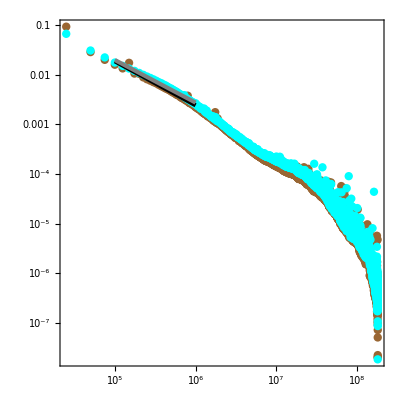

```mathematica
Show[{
ListLogLogPlot[contDistCondMeanScaled, PlotStyle->allTheme, AxesStyle->Directive[Black,Bold, 24], AxesOrigin->{7500,0}, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24], AspectRatio->1],
LogLogPlot[allContactF0Fit[[1]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[allContactF0Fit[[2]],{x,fitRange[[1]],fitRange[[2]]},  PlotStyle->fitTheme[[2]]]}, PlotRange->All]
```

#### Across Lads vs Not Lads

2

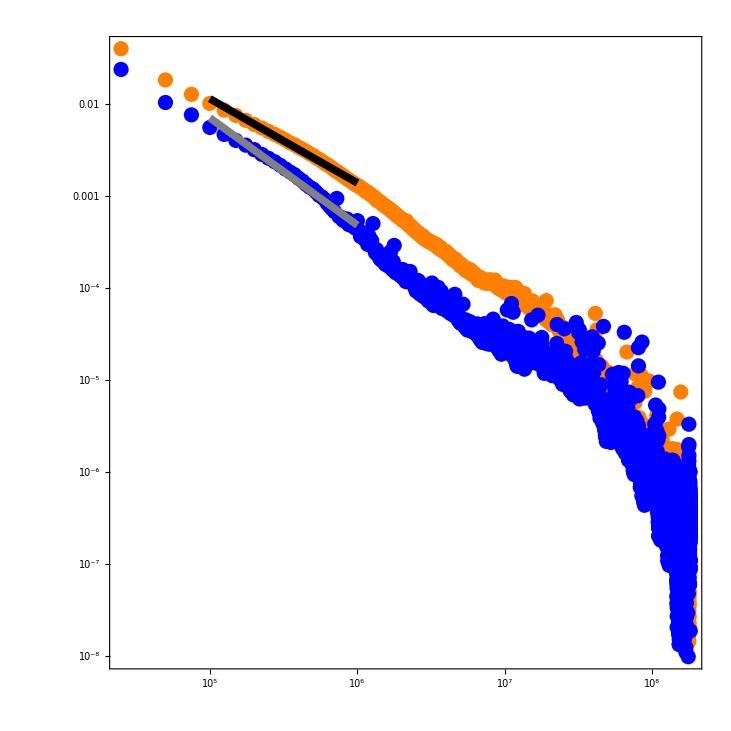

```mathematica
i=2
Show[{
ListLogLogPlot[acrossB1ChrVarDistSortMedianScaled[[i]], PlotStyle->insideTheme[[i]], AxesStyle->Directive[Black,Bold, 24]],
ListLogLogPlot[acrossNotB1ChrVarDistSortMedianScaled[[i]], PlotStyle->{outsideTheme[[i]]}, AxesStyle->Directive[Black,Bold, 24]],
LogLogPlot[acrossLadContactF0Fit[[i]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[acrossNotB1LadContactF0Fit[[i]],{x,fitRange[[1]],fitRange[[2]]},  PlotStyle->fitTheme[[2]]]

},PlotRange->All,AspectRatio->1, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30] ]
```

#### Within Lads vs outside Lads

1

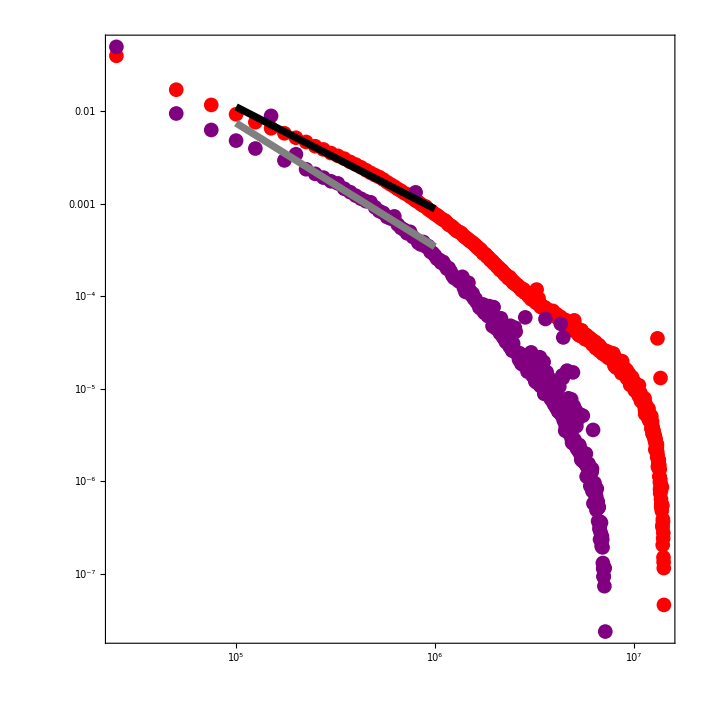

```mathematica
i=1
Show[{
ListLogLogPlot[withinB1ChrVarDistSortMedianScaled[[i]], PlotRange->All,PlotStyle->insideTheme[[i]], AxesStyle->Directive[Black,Bold, 24]],
ListLogLogPlot[withinNotB1ChrVarDistSortMedianScaled[[i]], PlotRange->All,PlotStyle->{outsideTheme[[i]]}, AxesStyle->Directive[Black,Bold, 24]],
LogLogPlot[withinLadContactF0Fit[[i]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[withinNotLadContactF0Fit[[i]],{x,fitRange[[1]],fitRange[[2]]},  PlotStyle->fitTheme[[2]]]

},PlotRange->All,AspectRatio->1, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24] ]
```

#### Within Lads Control vs KnockOut

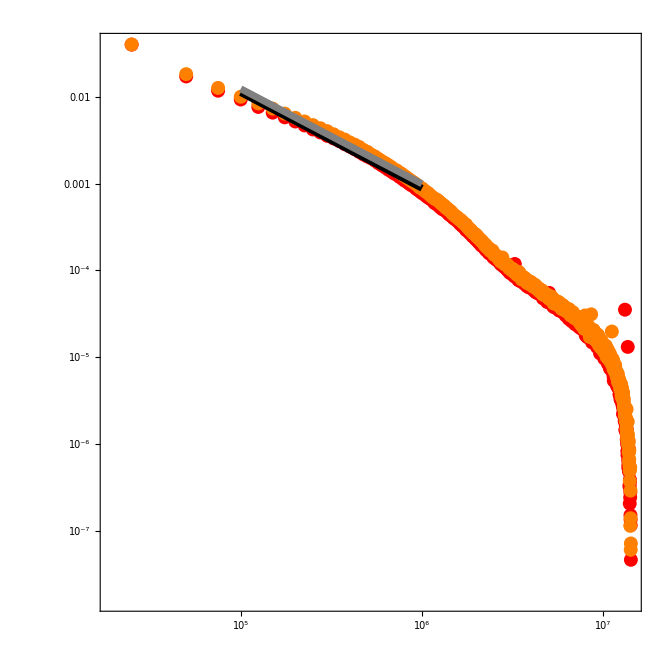

```mathematica
Show[{
ListLogLogPlot[withinB1ChrVarDistSortMedianScaled, PlotStyle->insideTheme, AxesStyle->Directive[Black,Bold, 24]],
LogLogPlot[withinLadContactF0Fit[[1]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[withinLadContactF0Fit[[2]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[2]]]
},AspectRatio->1, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24] ]
```

#### Within NotLads Control vs KnockOut

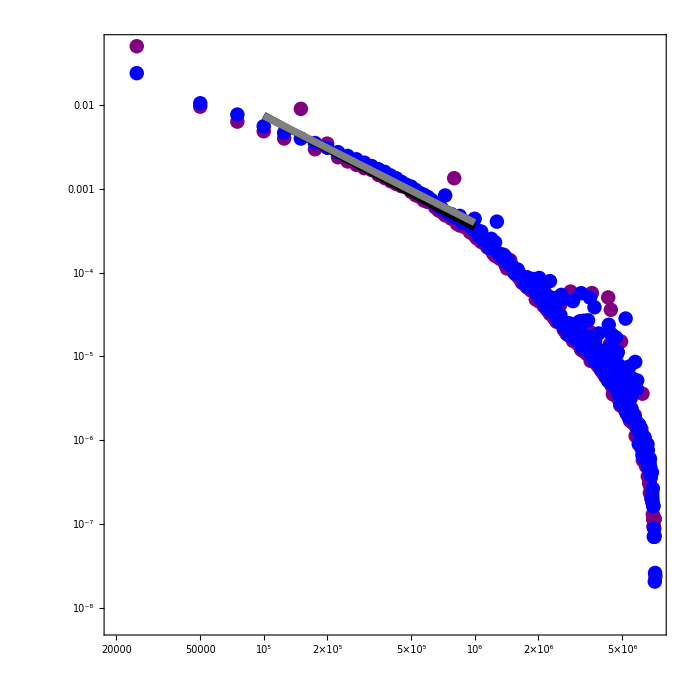

```mathematica
Show[{
ListLogLogPlot[withinNotB1ChrVarDistSortMedianScaled, PlotStyle->outsideTheme, AxesStyle->Directive[Black,Bold, 24]],
LogLogPlot[withinNotLadContactF0Fit[[1]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[withinNotLadContactF0Fit[[2]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[2]]]
},AspectRatio->1, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24] ]
```

#### Across Lads Control vs KnockOut

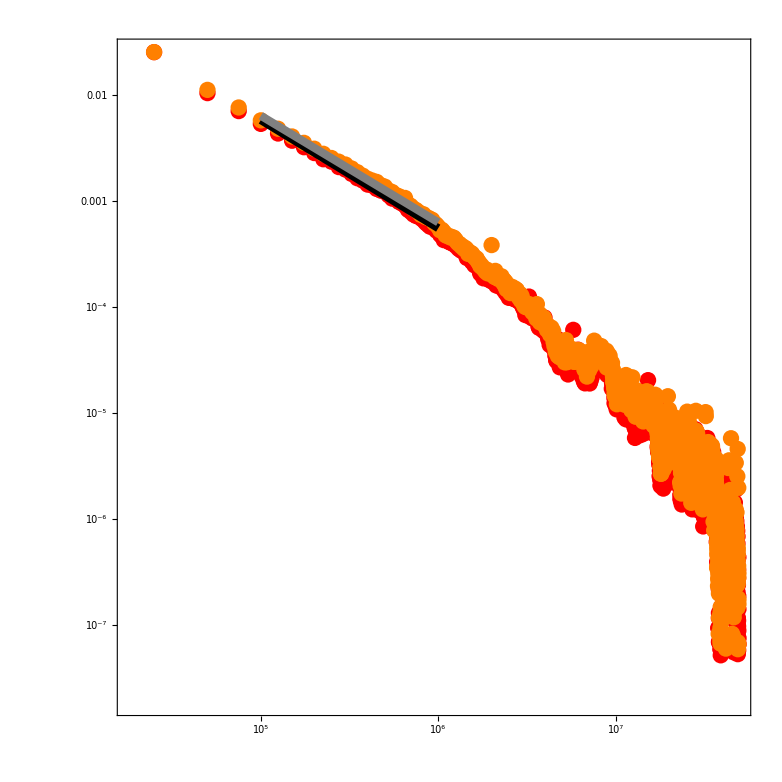

```mathematica
Show[{
ListLogLogPlot[acrossB1ChrVarDistSortMedianScaled, PlotStyle->insideTheme, AxesStyle->Directive[Black,Bold, 24]],
LogLogPlot[acrossLadContactF0Fit[[1]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[acrossLadContactF0Fit[[2]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[2]]]
},Ticks -> {ScientificForm[#]&},AspectRatio->1, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30] ]
```

#### Across NotLads Control vs KnockOut

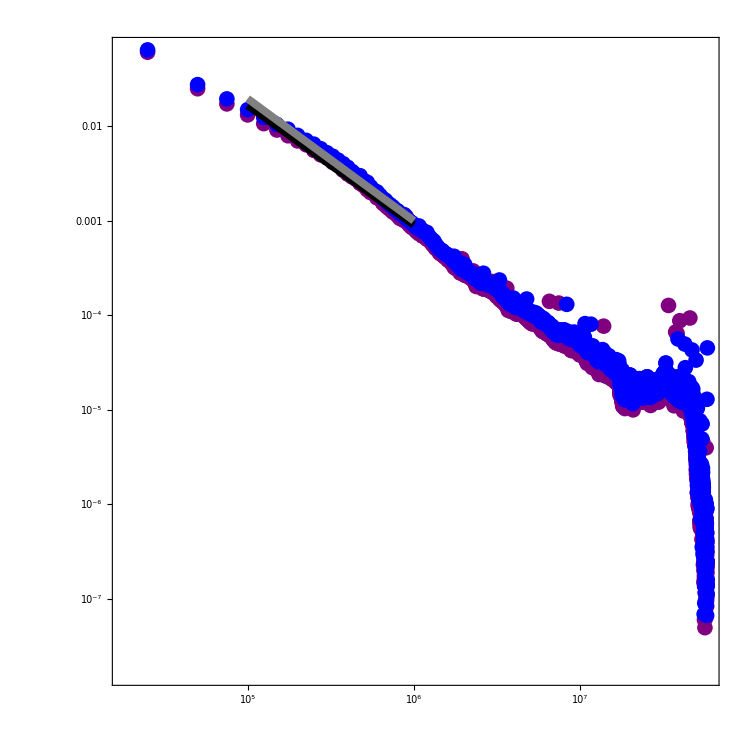

```mathematica
Show[{
ListLogLogPlot[acrossNotB1ChrVarDistSortMedianScaled, PlotStyle->outsideTheme, AxesStyle->Directive[Black,Bold, 24]],
LogLogPlot[acrossNotB1LadContactF0Fit[[1]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[1]]],
LogLogPlot[acrossNotB1LadContactF0Fit[[2]],{x,fitRange[[1]],fitRange[[2]]}, PlotStyle->fitTheme[[2]]]

},AspectRatio->1, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30] ]
```

### Without Fits

#### All Contacts on a chromosome

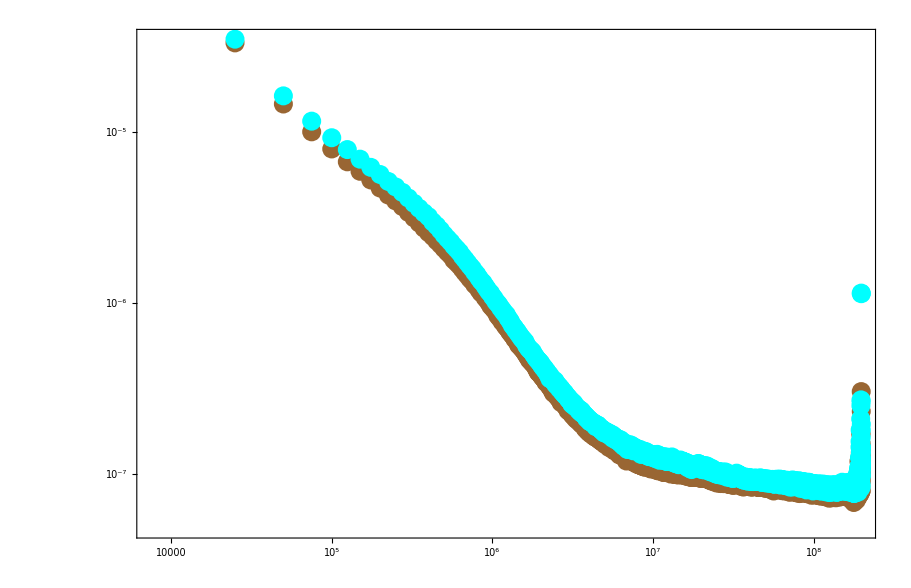

```mathematica
ListLogLogPlot[contDistCondMeanScaled, PlotRange->All, PlotStyle->allTheme, AxesStyle->Directive[Black,Bold, 24], AxesOrigin->{7500,0}, AspectRatio->Automatic, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24]]
```

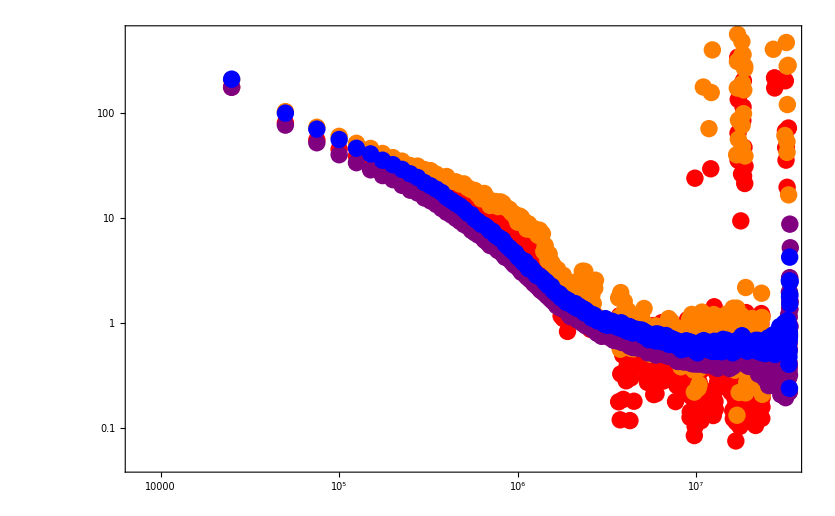

```mathematica
Show[
ListLogLogPlot[acrossB1ChrVarDistSortMedian, PlotRange->All, PlotStyle->insideTheme, AxesStyle->Directive[Black,Bold, 24], AxesOrigin->{7500,0}, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24]],

ListLogLogPlot[acrossNotB1ChrVarDistSortMedian, PlotRange->All, PlotStyle->outsideTheme, AxesStyle->Directive[Black,Bold, 24], AxesOrigin->{7500,0}, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,24]]
]
```

1

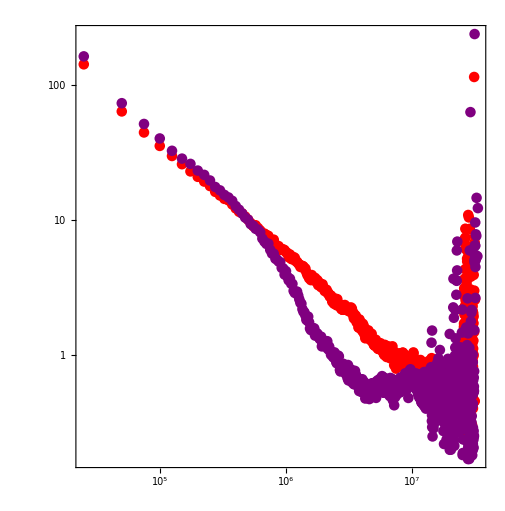

```mathematica
i=1
Show[{ListLogLogPlot[acrossB1ChrVarDistSortMedian[[i]], PlotRange->All, PlotStyle->insideTheme[[i]], AxesStyle->Directive[Black,Bold, 24]],
ListLogLogPlot[acrossNotB1ChrVarDistSortMedian[[i]], PlotRange->All, PlotStyle->{outsideTheme[[i]]}, AxesStyle->Directive[Black,Bold, 24]]

},PlotRange->All, AxesOrigin->{8.7,-1},AspectRatio->Automatic, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30] ]
```

#### Compare across LAD to across non-lad

1

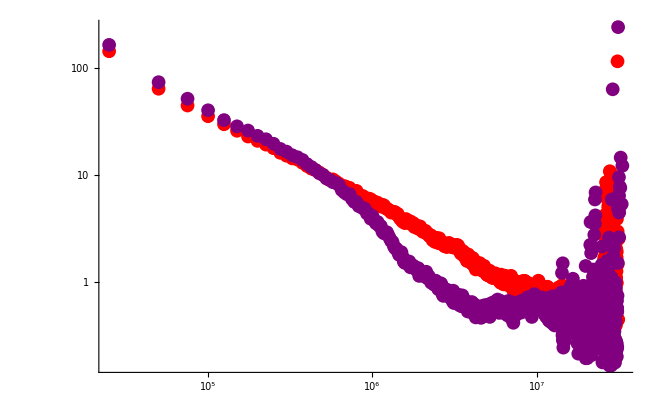

```mathematica
i=1
Show[{
ListLogLogPlot[acrossB1ChrVarDistSortMedian[[i]], PlotRange->All, PlotStyle->insideTheme[[i]], AxesStyle->Directive[Black,Bold, 24]],
ListLogLogPlot[acrossNotB1ChrVarDistSortMedian[[i]], PlotRange->All, PlotStyle->outsideTheme[[i]], AxesStyle->Directive[Black,Bold, 24]]

},PlotRange->All,AxesOrigin->{8.7,-1}]
```

#### Compare within lad to within inter-lad

2

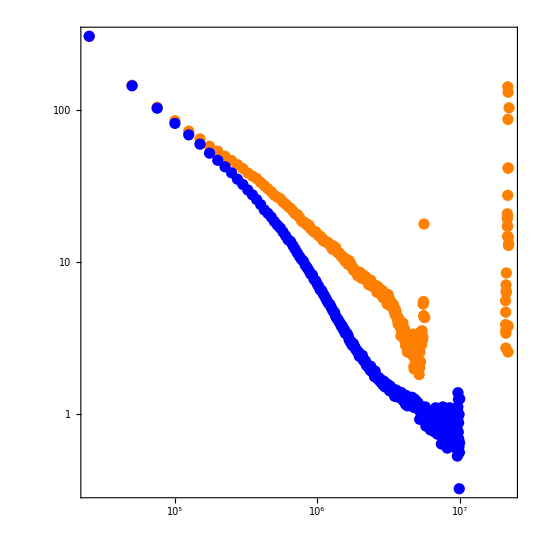

```mathematica
i=2
Show[{
ListLogLogPlot[withinB1ChrVarDistSortMedian[[i]], PlotRange->All, PlotStyle->insideTheme[[i]], AxesStyle->Directive[Black,Bold, 24]],
ListLogLogPlot[withinNotB1ChrVarDistSortMedian[[i]], PlotRange->All, PlotStyle->{outsideTheme[[i]]}, AxesStyle->Directive[Black,Bold, 24]]
},PlotRange->All, AxesOrigin->{8.7,-1},AspectRatio->Automatic, Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,30]]
```

#### Compare within a segment scaling

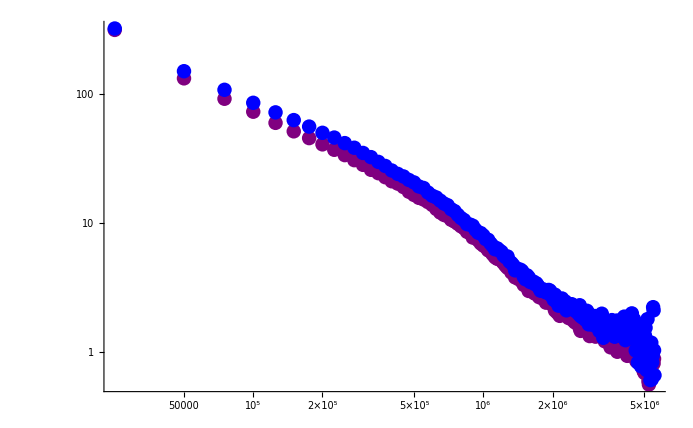

```mathematica
Show[{
ListLogLogPlot[withinNotB1ChrVarDistSortMedian, PlotRange->All, PlotStyle->outsideTheme, AxesStyle->Directive[Black,Bold, 24]]
},PlotRange->All, AxesOrigin->{8.7,-1}]
```

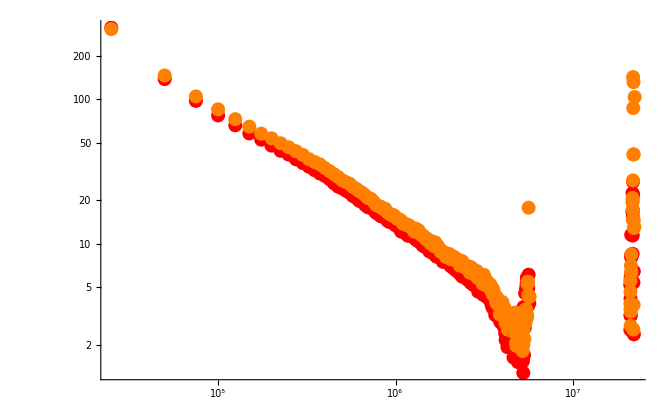

```mathematica
Show[{
ListLogLogPlot[withinB1ChrVarDistSortMedian, PlotRange->All, PlotStyle->insideTheme, AxesStyle->Directive[Black,Bold, 24]]
},PlotRange->All, AxesOrigin->{8.7,-1}]
```

## Testing

### Testing Contact Segmentation

```mathematica
vTest = Table[
overlapHicLadSelectByIndex[contactsByFirstPos[[1]],test[[i]],byChrB1[[chrToCheck,i]]],
{i,Length[test]}];
```

```mathematica
vTest1 =Table[distContact[Flatten[vTest[[i]],1]],{i,Length[vTest]}];
vTest2 = SplitBy[SortBy[Flatten[vTest1,1],1],#[[1]]&];
vTest3=Table[scalingEst[vTest2[[i]],Median[#]&],{i,Length[vTest2]}];
```

If you search by the index of the LAD positions (know that the dimensionality of the index corresponds to the according LAD, then you know you will obtain the same data!
If you flatten the index matrix for the LAD or non-LAD segments, it will search through and obtain the contacts for all of them that end in the LAD/segment of interest. This is a lot faster!

### Scaling Fits

lmFit = Table[{
   LinearModelFit[Log@contDistCondMeanScaled[[i, 4 ;; 41]], x, x],
   LinearModelFit[Log@contDistCondMeanScaled[[i, 41 ;; 200]], x, x],
   LinearModelFit[Log@contDistCondMeanScaled[[i, 201 ;; 4000]], x, x]
   }, {i, Length[contDistCondMean]}]

{{FittedModel[6.32023-0.928254 x],FittedModel[8.94738-1.13196 x],FittedModel[-6.37134-0.148023 x]},{FittedModel[6.47582-0.931879 x],FittedModel[8.95132-1.12681 x],FittedModel[-5.67054-0.186467 x]}}

f0Fit = Table[Normal[lmFit[[j, i]]] /. x -> Log[x] // Exp, {j, Length[lmFit]}, {i, Length[lmFit[[j]]]}]

{{555.702/x^0.928254,7687.76/x^1.13196,0.00170986/x^0.148023},{649.254/x^0.931879,7718.05/x^1.12681,0.003446/x^0.186467}}

### Alternate methods of analyzing scaling

contDistCondMeanScaled = resScalingContacts[contDistCondMean, segVal];

#### All Contacts

```mathematica
contDistCondMeanScaled = resScalingContacts[contDistCondMean];
```

```mathematica
allContactLmFit = lmFitHic[contDistCondMeanScaled,fitRange[[1]],fitRange[[2]]];
allContactF0Fit=f0FitHic[allContactLmFit];
```

```mathematica
dApproxAllCont = Table[3/allContactLmFit[[i,1,2,2]],{i,Length[allContactLmFit]}]
sValAllCont = Table[Abs[allContactLmFit[[i,1,2,2]]],{i,Length[allContactLmFit]}]
```

{-3.44819,-3.43914}

{0.87002,0.872311}

#### Within LAD

```mathematica
withinB1ChrVarDistSortMedianScaled = resScalingContacts[withinB1ChrVarDistSortMedian,segVal];
```

```mathematica
withinLadContactLmFit = lmFitHic[withinB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
withinLadContactF0Fit=f0FitHic[withinLadContactLmFit];
```

```mathematica
dApproxWithinLad = Table[3/withinLadContactLmFit[[i,1,2,2]],{i,Length[withinLadContactLmFit]}]
sValWithinLad = Table[Abs[withinLadContactLmFit[[i,1,2,2]]],{i,Length[withinLadContactLmFit]}]
```

{-3.75015,-3.74447}

{0.799968,0.801182}

#### Across LAD

```mathematica
acrossB1ChrVarDistSortMedianScaled = resScalingContacts[acrossB1ChrVarDistSortMedian,segVal];
```

```mathematica
acrossLadContactLmFit = lmFitHic[acrossB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
acrossLadContactF0Fit=f0FitHic[acrossLadContactLmFit];
```

```mathematica
dApproxAcrossLad = Table[3/acrossLadContactLmFit[[i,1,2,2]],{i,Length[acrossLadContactLmFit]}]
sValAcrossLad = Table[Abs[acrossLadContactLmFit[[i,1,2,2]]],{i,Length[acrossLadContactLmFit]}]
```

{-3.6029,-3.59972}

{0.832663,0.833397}

#### Within Not-LAD

```mathematica
withinNotB1ChrVarDistSortMedianScaled = resScalingContacts[withinNotB1ChrVarDistSortMedian,segVal];
```

```mathematica
withinNotLadContactLmFit = lmFitHic[withinNotB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
withinNotLadContactF0Fit=f0FitHic[withinNotLadContactLmFit];
```

```mathematica
dApproxWithinNotLad = Table[3/withinNotLadContactLmFit[[i,1,2,2]],{i,Length[withinLadContactLmFit]}]
sValWithinNotLad = Table[Abs[withinNotLadContactLmFit[[i,1,2,2]]],{i,Length[withinLadContactLmFit]}]
```

{-3.25279,-3.22353}

{0.922284,0.930657}

#### Across Not-LAD

```mathematica
acrossNotB1ChrVarDistSortMedianScaled = resScalingContacts[acrossNotB1ChrVarDistSortMedian,segVal]
```

{{{0,0.150348},{25000,0.0390477},{50000,0.0169527},{75000,0.0114976},{100000,0.00915724},{125000,0.00775864},{150000,0.00678036},7468,{187650000,0.0000963998},{187675000,0.000157348},{187700000,0.0000746463},{187725000,0.000139772},{187750000,0.000165498},{187800000,0.000141452},{187975000,0.000108401}},{1}}
 |  |  |  |

```mathematica
acrossNotB1LadContactLmFit = lmFitHic[acrossNotB1ChrVarDistSortMedianScaled,fitRange[[1]],fitRange[[2]]];
acrossNotB1LadContactF0Fit=f0FitHic[acrossNotB1LadContactLmFit];
```

```mathematica
dApproxAcrossNotLad = Table[3/acrossNotB1LadContactLmFit[[i,1,2,2]],{i,Length[withinLadContactLmFit]}]
sValAcrossNotLad = Table[Abs[acrossNotB1LadContactLmFit[[i,1,2,2]]],{i,Length[withinLadContactLmFit]}]
```

{-3.24168,-3.18723}

{0.925445,0.941255}